Lukas Bundrock, Alexandre Girouard, Denis S. Grebenkov, Michael Levitin, and Iosif Polterovich

# Exterior Steklov problem for spheroids

## Script accompanying the paper The exterior Steklov problem for Euclidean domains

## Auxiliary

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{amsmath}","\\usepackage{fourier}",
"\\usepackage[lining]{ebgaramond}",
 "\usepackage[scr=boondox]{mathalpha}",
"\\usepackage{xcolor}\\definecolor{darkgreen}{rgb}{0.00, 0.67, 0.00}"},FontSize->12,Magnification->1];
clr=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Bounds

```mathematica
ellipsoid[a_,b_,c_][x_,y_,z_]:=(x/a)^2+(y/b)^2+(z/c)^2-1;
curvaturesprolate=-FullSimplify[Simplify[ResourceFunction["PrincipalCurvatures"][ellipsoid[a,a,1][x,y,z],{x,y,z}],0<a<=1]/.y^2->a^2(1-z^2)-x^2, 0<a<=1&&-1<=z<=1]
curvaturesoblate=-FullSimplify[Simplify[ResourceFunction["PrincipalCurvatures"][ellipsoid[1,1,a][x,y,z],{x,y,z}],0<a<=1]/.y^2->1-x^2-z^2/a^2, 0<a<1&&-a<=z<=a]
νprolate=Grad[ellipsoid[a,a,1][x,y,z], {x,y,z}]
XiXiargprolate=Simplify[{x,y,z}.νprolate/Norm[νprolate]/Norm[{x,y,z}]^2, ellipsoid[a,a,1][x,y,z]==0&&0<a<1]/.{Abs[zz_]^2->zz^2}/.y^2->a^2(1-z^2)-x^2 
XiXi=XiXiprolate=Simplify[Minimize[{XiXiargprolate,0<a<1, -1<=z<=1}, z],0<a<1][[1]]
νoblate=Grad[ellipsoid[1,1,a][x,y,z], {x,y,z}]
XiXiargoblate=Simplify[{x,y,z}.νoblate/Norm[νoblate]/Norm[{x,y,z}]^2, ellipsoid[1,1,a][x,y,z]==0&&0<a<1]/.{Abs[zz_]^2->zz^2}/.x^2->1-y^2-z^2/a^2 
XiXioblate=Simplify[Minimize[{%,0<a<1, -a<=z<=a}, z],0<a<1][[1]];
XiXioblate-XiXi
```

{a/((1+(-1+a^2) z^2)^(3/2)),1/(a √(1+(-1+a^2) z^2))}

{a^2/(√(a^4+z^2-a^2 z^2)),a^4/((a^4+z^2-a^2 z^2)^(3/2))}

{(2 x)/a^2,(2 y)/a^2,2 z}

a^2/((z^2+a^2 (1-z^2)) √(a^4 z^2+a^2 (1-z^2)))

Piecewise[{{1, a>1/(√2)}, {(3 √3 a)/(2 (1+a^2)^(3/2)), True}}]

{2 x,2 y,(2 z)/a^2}

1/((1+z^2-z^2/a^2) √(1+z^2/a^4-z^2/a^2))

0

## Prolate

The method of eigenvalue calculations follows the paper  D. S. Grebenkov, Spectral properties of the Dirichlet-to-Neumann operator for spheroids. Phys. Rev. E 109:5, article 055306 (2024).

```mathematica
α0 = ArcTanh[a];
coshα0=Cosh[α0];
sinhα0=Sinh[α0];
LegQ[0,z_]:=1/2Log[(z+1)/(z-1)];
LegQ[1,z_]:=z LegQ[0,z]-1;
LegQ[n_,z_]:=(2n-1)/n z LegQ[n-1,z]-(n-1)/n LegQ[n-2,z];
DLegQ[n_,z_]:=(n+1)/(z^2-1)(LegQ[n+1,z]-z LegQ[n,z]);
aE= Sqrt[1-a^2];
```

```mathematica
FFF[n_, n1_,z_]:=Integrate[LegendreP[n,x] LegendreP[n1,x]/ Sqrt[z^2-x^2], {x,-1,1}, Assumptions->z>1 && n∈ Integers && n1∈ Integers && n>=0 && n1>=0]
```

```mathematica
Nmax=10;
```

```mathematica
TFFF=Table[If[OddQ[n+n1],0,FFF[n, n1, z]], {n,0,Nmax}, {n1,0,Nmax}];
TDLegQ=Table[DLegQ[n1, coshα0], {n1,0,Nmax}];
TLegQ=Table[LegQ[n1,coshα0], {n1,0,Nmax}];
```

```mathematica
Tb=Table[If[OddQ[n+n1],0,Simplify[-Sqrt[(n+1/2)(n1+1/2)]  TDLegQ[[n1+1]]/TLegQ[[n1+1]] TFFF[[n+1, n1+1]]/.z-> coshα0]], {n,0,Nmax}, {n1,0,Nmax}];
```

## Oblate

```mathematica
TDLegQoblate=Table[DLegQ[n1, I sinhα0], {n1,0,Nmax}];
TLegQoblate=Table[LegQ[n1,I sinhα0], {n1,0,Nmax}];
Tboblate=Table[If[OddQ[n+n1],0,Simplify[ Sqrt[(n+1/2)(n1+1/2)]  TDLegQoblate[[n1+1]]/TLegQoblate[[n1+1]] TFFF[[n+1, n1+1]]/.z-> I sinhα0]], {n,0,Nmax}, {n1,0,Nmax}];
```

## Plotting

```mathematica
legtextprolate=MaTeX[{"\\text{numerical }\\sigma_1\\left(\\mathcal{P}_a^\\mathrm{ext}\\right)", "\\beta\\left(\\mathscr{p}_a\\right)", "\\beta_\\mathrm{X}\\left(\\mathscr{p}_a\\right)"}];
legtextoblate=MaTeX[{"\\text{numerical }\\sigma_1\\left(\\mathcal{O}_a^\\mathrm{ext}\\right)", "\\beta\\left(\\mathscr{o}_a\\right)", "\\beta_\\mathrm{X}\\left(\\mathscr{o}_a\\right)"}];
legtextprolatescaled=MaTeX[{"\\text{numerical }\\sigma_1\\left(\\widetilde{\\mathcal{P}}_a^\\mathrm{ext}\\right)", "\\beta\\left(\\widetilde{\\mathscr{p}}_a\\right)", "\\beta_\\mathrm{X}\\left(\\widetilde{\\mathscr{p}}_a\\right)"}];
tsxp={0, 0.5, 1};tsyp={5, 10}; tprolate={{tsxp, MaTeX[tsxp]}//Transpose,{tsyp, MaTeX[tsyp]}//Transpose};
tsxo={0, 0.5, 1};tsyo={0.5, 1}; toblate={{tsxo, MaTeX[tsxo]}//Transpose,{tsyo, MaTeX[tsyo]}//Transpose};
```

```mathematica
(* we have to approximate near a=1 *)
prolateactualnearball= Join[Table[{a,Eigenvalues[Tb,-1][[1]]sinhα0/aE},{a, {0.945}}],{{1,1}}];
prolatevolumescalednearball={prolateactualnearball[[;;,1]],prolateactualnearball[[;;,1]]^(2/3)prolateactualnearball[[;;,2]]}//Transpose;
```

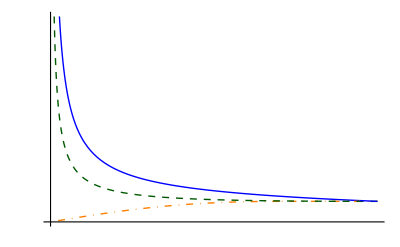

```mathematica
figprolateactual=Legended[Show[Plot[Eigenvalues[sinhα0/aE Tb,-1][[1]],{a,0.0001,0.945},PlotPoints->100, PlotStyle->{Thick,Blue},PlotRange->{0,10}],Plot[ XiXi, {a,0,1}, PlotStyle->{Thick, DotDashed,Orange}],
Plot[(1-a^2)/(-2a Log[a]), {a,0.0001,0.9999}, PlotStyle->{Thick,Dashed, DarkGreen},PlotRange->{0,10}],
ListLinePlot[prolateactualnearball, PlotStyle->{Thick,Blue}], AxesOrigin->{0,0}, PlotRange->All,AxesLabel->{MaTeX["a"], None},Ticks->tprolate], Placed[LineLegend[{Directive[Blue,Thick],Directive[Dashed, DarkGreen,Thick], Directive[DotDashed,Orange, Thick]}, legtextprolate],After]]
```

```mathematica
Export["figprolateactual.pdf",figprolateactual]
```

figprolateactual.pdf

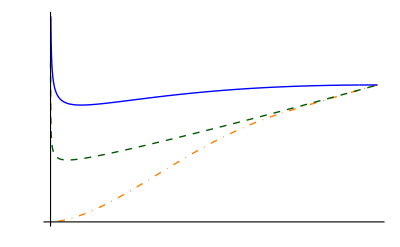

```mathematica
figprolatescaled=Legended[Show[Plot[a^(2/3)Eigenvalues[sinhα0/aE Tb,-1][[1]],{a,0.0001,0.945},PlotPoints->100, PlotStyle->{Thick,Blue},PlotRange->{0,1.5}],Plot[a^(2/3)XiXi, {a,0,1}, PlotStyle->{Thick, DotDashed,Orange}],
Plot[a^(2/3)(1-a^2)/(-2a Log[a]), {a,0.0001,0.9999}, PlotStyle->{Thick,Dashed, DarkGreen},PlotRange->{0,1.5}],
ListLinePlot[prolatevolumescalednearball, PlotStyle->{Thick,Blue}], AxesOrigin->{0,0}, PlotRange->All,AxesLabel->{MaTeX["a"], None},Ticks->toblate], Placed[LineLegend[{Directive[Blue,Thick],Directive[Dashed, DarkGreen,Thick], Directive[DotDashed,Orange, Thick]}, legtextprolatescaled],After]]
```

```mathematica
asmall= Table[b,{b, 10^(-8), 10^(-6),2 10.^(-8)}];
evsmall= Table[{a,a^(2/3) Eigenvalues[sinhα0/aE Tb,-1][[1]]},{a,asmall}];
```

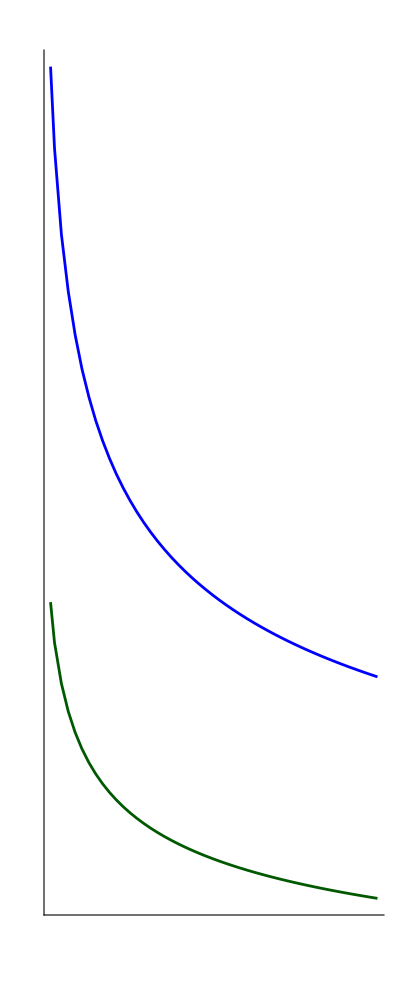

```mathematica
smallt=MaTeX[{"\\small{5\\times 10^{-7}}","\\small{10^{-6}}"}]; 
smallprolate=Show[ListLinePlot[evsmall, PlotStyle->Blue],
ListLinePlot[Table[{a,(1-a^2)/(-2a^(1/3) Log[a])}, {a,asmall}], PlotStyle->DarkGreen],
 PlotRange->All,AxesOrigin->{0,3}, AspectRatio->2.5, Ticks->{{{5 10^(-7),10^(-6)}, smallt}//Transpose,{{5,10,15},MaTeX[{5,10,15}]}//Transpose}]
```

```mathematica
figprolatescaledwithinset=Show[figprolatescaled,ImagePadding->{{140,Automatic},{Automatic, Automatic}}, Epilog->{Inset[Framed[smallprolate], {-0.12,0},Scaled[{1,0}],Scaled[1]]},PlotRangeClipping->False, AspectRatio->1]
```

-Graphics-

```mathematica
Export["figprolatescaledwithinset.pdf",figprolatescaledwithinset]
```

figprolatescaledwithinset.pdf

```mathematica
oblateactualnearball=Append[Table[{a,coshα0/aE Eigenvalues[ Tboblate,-1][[1]]},{a, {0.945}}], {1,1}]
```

{{0.945,1.01859},{1,1}}

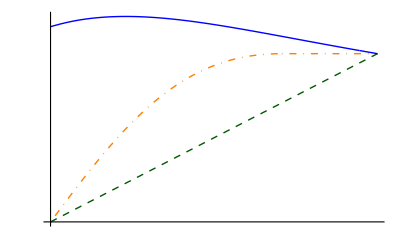

```mathematica
figoblateactual=Legended[Show[Plot[Eigenvalues[coshα0/aE Tboblate,-1][[1]],{a,0.0001,0.945},PlotPoints->100, PlotStyle->{Thick,Blue}],Plot[ XiXioblate, {a,0,1}, PlotStyle->{{Thick,DotDashed,Orange}}],
Plot[a, {a,0,1}, PlotStyle->{Thick,Dashed, DarkGreen}],
ListLinePlot[oblateactualnearball, PlotStyle->{Thick,Blue}],
AxesOrigin->{0,0}, PlotRange->All,AxesLabel->{MaTeX["a"], None},Ticks->toblate], Placed[LineLegend[{Directive[Blue,Thick],Directive[Dashed, DarkGreen,Thick], Directive[DotDashed,Orange, Thick]}, legtextoblate],After]]
```

```mathematica
Export["figoblateactual.pdf",figoblateactual]
```

figoblateactual.pdf